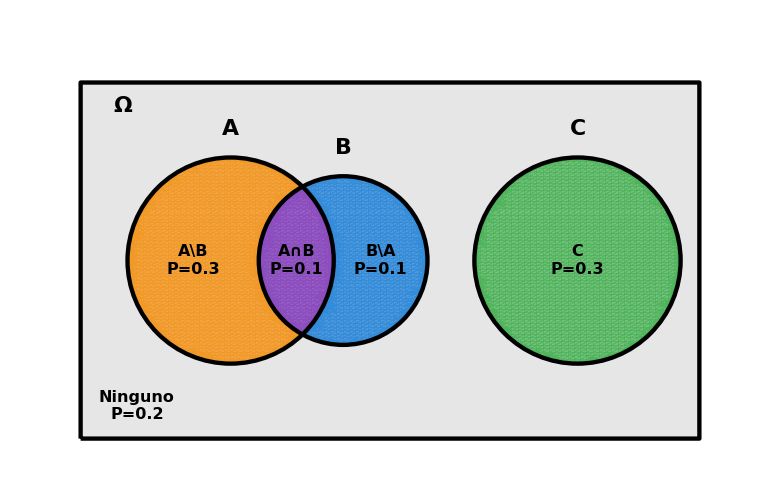

```mathematica
(*Datos del problema*)PA=0.4;PB=0.2;PC=0.3;PAB=0.1;

(*Cantidades derivadas para los nueve apartados,calculadas automáticamente*)
PAsoloB=PA-PAB;                      (*a) solo A*)
PBsoloA=PB-PAB;                      (*B\A,usada en h)*)
PABC=0;                                (*b) los tres*)
PAyBnoC=PAB;                           (*c)*)
Atleast2=PAB;                          (*d)*)
Exactly2=Atleast2-PABC;              (*e)*)
NoMoreThan2=1-PABC;                  (*f)*)
PUnionAB=PA+PB-PAB;
Atleast1=PUnionAB+PC;                (*g)*)
Exactly1=Atleast1-Atleast2;          (*h)*)
Pfuera=1-Atleast1;                   (*i)*)

(*Geometría:A y B solapados;C completamente separado*)
cA={-1.7,0};rA=1.1;
cB={-0.5,0};rB=0.9;
cC={2.0,0};rC=1.1;

limX=3.3;limY=1.9;

colorA=RGBColor[0.95,0.6,0.15];    (*A\B-naranja*)
colorAB=RGBColor[0.55,0.3,0.75];   (*A∩B-morado*)
colorB=RGBColor[0.2,0.55,0.85];    (*B\A-azul*)
colorC=RGBColor[0.3,0.7,0.35];     (*C-verde*)
colorFuera=RGBColor[0.9,0.9,0.9];  (*ninguno-gris*)

grafico=Show[Graphics[{colorFuera,Rectangle[{-limX,-limY},{limX,limY}]}],RegionPlot[(x-cA[[1]])^2+y^2<rA^2&&!((x-cB[[1]])^2+y^2<rB^2),{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorA,Opacity[0.85]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[(x-cA[[1]])^2+y^2<rA^2&&(x-cB[[1]])^2+y^2<rB^2,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorAB,Opacity[0.9]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[(x-cB[[1]])^2+y^2<rB^2&&!((x-cA[[1]])^2+y^2<rA^2),{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorB,Opacity[0.85]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[(x-cC[[1]])^2+y^2<rC^2,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorC,Opacity[0.75]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],Graphics[{FaceForm[None],EdgeForm[{Black,Thickness[0.004]}],Rectangle[{-limX,-limY},{limX,limY}],Black,Thickness[0.004],Circle[cA,rA],Circle[cB,rB],Circle[cC,rC],(*Letras A,B,C encima de cada círculo,bien separadas entre sí*)Text[Style["A",22,Bold],{cA[[1]],rA+0.3}],Text[Style["B",22,Bold],{cB[[1]],rB+0.3}],Text[Style["C",22,Bold],{cC[[1]],rC+0.3}],(*Ω en la esquina superior izquierda,lejos de cualquier otra etiqueta*)Text[Style["Ω",22,Bold],{-limX+0.45,limY-0.25}],(*Valores de las cinco regiones primitivas,centrados en su región*)Text[Style["A\\B\nP="<>ToString[PAsoloB],16,Bold],{-2.1,0}],Text[Style["A∩B\nP="<>ToString[PAB],16,Bold],{-1.0,0}],Text[Style["B\\A\nP="<>ToString[PBsoloA],16,Bold],{-0.1,0}],Text[Style["C\nP="<>ToString[PC],16,Bold],{cC[[1]],0}],(*"Ninguno" en la esquina inferior izquierda,lejos de Ω*)Text[Style["Ninguno\nP="<>ToString[Pfuera],16,Bold],{-limX+0.6,-limY+0.35}]}],PlotRange->{{-limX-0.1,limX+0.1},{-limY-0.1,limY+0.4}},AspectRatio->Automatic,ImageSize->780];

grafico
```

```mathematica
Export["prob_quesada_2_8_a.png",grafico,Background->None,ImageResolution->600];
```